#### Limits and ranges

```mathematica
peakNormedNormalDistribution[c,s,t]
```

ⅇ^(-1/2 (-128+t)^2)

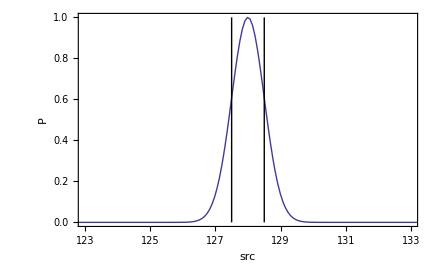
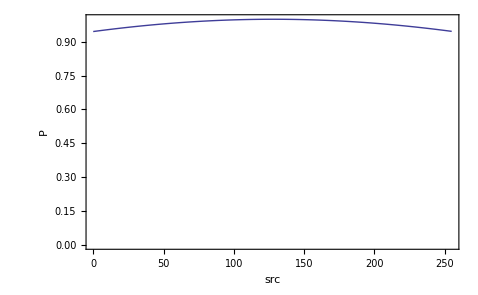
-Graphics- | -Graphics-
 | 0-1 | 0 - 255
Mean | 0 | 0
Std | 1/510 | 1/2
G | 255 √2 | √2 |  | 0-1 | 0 - 255
Mean | 1 | 255
Std | 3/2 | 765/2
G | (√2)/3 | (√2)/765

```mathematica
sMin=0;sMax=255;
dMin=0;dMax=255;
ssMin=1/2; ssMax=3/2 255 ;
Grid[{{
c=128;s=ssMin;
Plot[peakNormedNormalDistribution[c,s,t],{t,sMin,sMax},PlotRange->{{c-5,c+5},All},ImageSize->{200,200},FrameTicks->{Table[i,{i,c-5,c+5}],Automatic},Epilog-> {{Line[{{c-0.5,0},{c-0.5,1}}],Line[{{c+0.5,0},{c+0.5,1}}]}},Frame->True,FrameLabel->{{"P",None},{"src",Row[{"s =" ,s}]}},ImageSize->400],
c=128;s=N[ssMax];
Plot[peakNormedNormalDistribution[c,s,t],{t,sMin,sMax},PlotRange->{{sMin,sMax},{0,1}},ImageSize->{200,200},Frame->True,FrameLabel->{{"P",None},{"src",Row[{"s =" ,s}]}},ImageSize->400]},
{valTable[setDistroValues[{{0,sMin},{σMin,ssMin},{γMax,1}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False],{{sMin,sMax},{dMin,dMax}}],
valTable[setDistroValues[{{1,sMax},{σMax,ssMax},{γMax,gMax}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False],{{sMin,sMax},{dMin,dMax}}]}
}]
Clear[x,s,g,c,sMin,sMax,dMin,dMax]
```

therefore usefully 0.5 <=  s <= 255/2

```mathematica
sMin=0;sMax=255;
dMin=0;dMax=255;
ssMin=1/2; ssMax=255/2 ;
{{μMin,cMin},{σMin,ssMin},{γMax,gMax}}=N[setDistroValues[{{0,sMin},{σMin,ssMin},{γMax,1}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];
{{μMax,cMax},{σMax,ssMax},{γMin,gMin}}=N[setDistroValues[{{1,sMax},{σMax,ssMax},{γMax,gMax}},{{sMin,sMax},{dMin,dMax}},Unit->False,G->False]];
Framed[valTable[{{μMin≤ "μ"≤μMax,cMin≤ "c"≤cMax},{σMin≤ "σ"≤σMax,ssMin≤ "s"≤ssMax},{γMin≤ "γ"≤γMax,gMin≤ "g"≤gMax}},{{sMin,sMax},{dMin,dMax}}]]
```

| 0-1 | 0 - 255
Mean | 0.≤μ≤1. | 0.≤c≤255.
Std | 0.001961≤σ≤0.5 | 0.5≤s≤127.5
G | 1.414≤γ≤360.6 | 0.005546≤g≤1.414

Lowest limit on σ is when s=1/2
1/(2 sRange) < σ < 1/2
0 < μ< 1

```mathematica
uG[1/2]
```

√2

upper limit of σ is when the gradient at the mean equals (dMax-dMin)/(sMax-sMin) at least closely  enough that the deflection is inperceptable in the finite representation.

```mathematica
diag[x_,sMin_,sMax_,dMin_,dMax_]:=(dMax-dMin)x/(sMax-sMin)+(dMin sMax-dMax sMin)/(sMax-sMin)
```

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;Dynamic[Plot[{dis[ x,s,c,sMin,sMax,dMin,dMax],diag[x,sMin,sMax,dMin,dMax]},{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{dMin,dMax}}]])&}]
```

```mathematica
sigMax[c_,{{sMin_,sMax_},{dMin_,dMax_}}]:=3/32 √((dMax-dMin) (sMax-sMin) (sMax-sMin+6 Abs[-2 c+sMax+sMin]))
```

```mathematica
sigMax[c_,{{sMin_,sMax_},{dMin_,dMax_}}]:=3/32 √((dMax-dMin) (sMax-sMin) (sMax-sMin+6.2 Abs[-2 c+sMax+sMin]))
```

```mathematica
6.2^2
```

38.44

```mathematica
N[Sqrt[32]]
```

5.65685

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;Dynamic[Plot[{Abs[dis[ x, sigMax[c,{{sMin,sMax},{dMin,dMax}}],c,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax]],1,2,3,4,5,6,7,8},{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{0,1.2}}]])&}]
```

```mathematica
err[x_,c_,{{sMin_,sMax_},{dMin_,dMax_}}]:=FullSimplify[Abs[dis[ x, sigMax[{{sMin,sMax},{dMin,dMax}}],c,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax]]]
```

```mathematica
err[x_,c_,{{sMin_,sMax_},{dMin_,dMax_}}]:=Abs[(dMax-dMin) ((sMin-x)/(sMax-sMin)+(-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]+Erf[(√2 (c-x))/(3 √(dMax-dMin) √(sMax-sMin))])/(Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))];
```

```mathematica
err[x_,c_,{{sMin_,sMax_},{dMin_,dMax_}}]:=Abs[(dMax-dMin) ((sMin-x)/(sMax-sMin)+(-Erf[κ (c-sMin)]+Erf[κ (c-x)])/(Erf[κ (c-sMax)]-Erf[κ(c-sMin)]))]
```

```mathematica
κ[{{sMin_,sMax_},{dMin_,dMax_}}]:=(√2)/(3 √(dMax-dMin) √(sMax-sMin));

Series[Erf[κ (c-x)],{x,(c+sMax)/2,5}]
```

Erf[1/2 (c κ-sMax κ)]-(2 (ⅇ^(-1/4 (c-sMax)^2 κ^2) κ) (x-(c+sMax)/2))/(√π)+(ⅇ^(-1/4 (c-sMax)^2 κ^2) (-c+sMax) κ^3 (x-(c+sMax)/2)^2)/(√π)-((ⅇ^(-1/4 (c-sMax)^2 κ^2) κ^3 (-2+(c κ-sMax κ)^2)) (x-(c+sMax)/2)^3)/(3 √π)-((ⅇ^(-1/4 (c-sMax)^2 κ^2) (c-sMax) κ^5 (-6+c^2 κ^2-2 c sMax κ^2+sMax^2 κ^2)) (x-(c+sMax)/2)^4)/(12 √π)-1/(10 √π)(ⅇ^(-1/4 (c-sMax)^2 κ^2) κ^5 (2-(c-sMax)^2 κ^2+1/6 (c-sMax)^2 κ^2 (-6+c^2 κ^2-2 c sMax κ^2+sMax^2 κ^2))) (x-(c+sMax)/2)^5+O[x-(c+sMax)/2]^6

```mathematica
Expand[(dMax-dMin) ((sMin-x)/(sMax-sMin)+(-Erf[κ (c-sMin)]+Series[Erf[κ (c-x)],{x,(c+sMax)/2,5}])/(Erf[κ (c-sMax)]-Erf[κ(c-sMin)]))]
```

(dMax-dMin) ((-c/2-sMax/2+sMin)/(sMax-sMin)+(-Erf[(c-sMin) κ]+Erf[1/2 (c κ-sMax κ)])/(Erf[(c-sMax) κ]-Erf[(c-sMin) κ]))+(dMax-dMin) (1/(-sMax+sMin)-(2 ⅇ^(-1/4 (c-sMax)^2 κ^2) κ)/(√π (Erf[(c-sMax) κ]-Erf[(c-sMin) κ]))) (x-(c+sMax)/2)+((dMax-dMin) ⅇ^(-1/4 (c-sMax)^2 κ^2) (-c+sMax) κ^3 (x-(c+sMax)/2)^2)/(√π (Erf[(c-sMax) κ]-Erf[(c-sMin) κ]))-(((dMax-dMin) ⅇ^(-1/4 (c-sMax)^2 κ^2) κ^3 (-2+(c κ-sMax κ)^2)) (x-(c+sMax)/2)^3)/(3 (√π (Erf[(c-sMax) κ]-Erf[(c-sMin) κ])))-(((dMax-dMin) ⅇ^(-1/4 (c-sMax)^2 κ^2) (c-sMax) κ^5 (-6+c^2 κ^2-2 c sMax κ^2+sMax^2 κ^2)) (x-(c+sMax)/2)^4)/(12 (√π (Erf[(c-sMax) κ]-Erf[(c-sMin) κ])))-(((dMax-dMin) ⅇ^(-1/4 (c-sMax)^2 κ^2) κ^5 (2-(c-sMax)^2 κ^2+1/6 (c-sMax)^2 κ^2 (-6+c^2 κ^2-2 c sMax κ^2+sMax^2 κ^2))) (x-(c+sMax)/2)^5)/(10 (√π (Erf[(c-sMax) κ]-Erf[(c-sMin) κ])))+O[x-(c+sMax)/2]^6

```mathematica
DynamicDistroPanel[{({{μ,c},{σ,s},{γ,g}}=#1;{{sMin,sMax},{dMin,dMax}}=#2;Dynamic[Plot[{MaxVal[err[x,c,{{sMin,sMax},{dMin,dMax}}],x],1,2,3,4,5,6,7,8},{c,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{0,8}}]])&}]
```

```mathematica
pts=Table[Maximize[{err[x,c,{{0,255},{0,255}}],x≥ 0&&x≤255},x],{c,1,255}];
npts=Map[({x/.#[[2]],#[[1]]})&,pts];
```

$Aborted

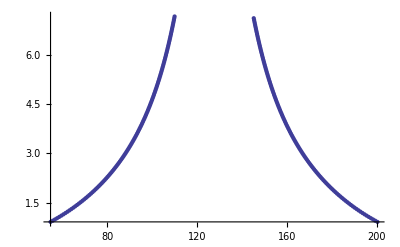

```mathematica
ListPlot[npts,PlotRange->All]
```

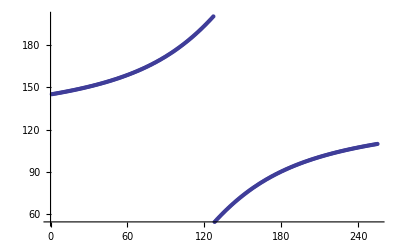
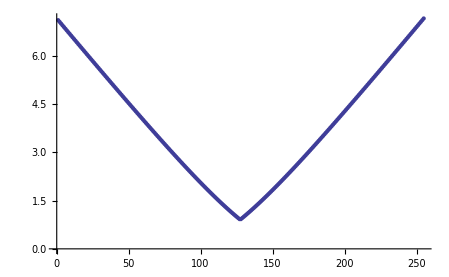

```mathematica
xpts=npts[[All,1]];
cpts=npts[[All,2]];
{ListPlot[xpts],ListPlot[cpts]}
```

```mathematica
fitPts = Transpose[{xpts[[128;;255]],Table[i,{i,128,255}]}];
```

```mathematica
fitPts[[1]]
```

{1/2 (256-765 √(3 Log[2]-2 Log[3]-Log[π]-2 Log[Erf[(127 √2)/765]+Erf[(128 √2)/765]])),128}

```mathematica
fit=Fit[xpts[[128;;255]],{1,Log[c]},c]
FindFit[fitPts,a Log[b+c x],{a,b,c},x]
```

28.7547+15.9916 Log[c]

FindFit::nrlnum: The function value {803.769  + 302.295\ ⅈ, 803.715  + 302.295\ ⅈ, 803.64  + 302.295\ ⅈ, 803.544  + 302.295\ ⅈ, 803.427  + 302.295\ ⅈ, 803.29  + 302.295\ ⅈ, 803.133  + 302.295\ ⅈ, « 38 », 785.864  + 302.295\ ⅈ, 785.216  + 302.295\ ⅈ, 784.562  + 302.295\ ⅈ, 783.9  + 302.295\ ⅈ, 783.232  + 302.295\ ⅈ, « 78 »} is not a list of real numbers with dimensions {128} at {a, b, c} = {96.2234, -7263.08, -160.738}.

{a→96.2234,b→-7263.08,c→-160.738}

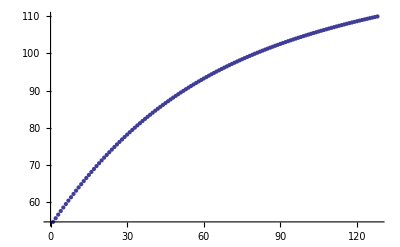

```mathematica
ListPlot[xpts[[128;;255]]]
```

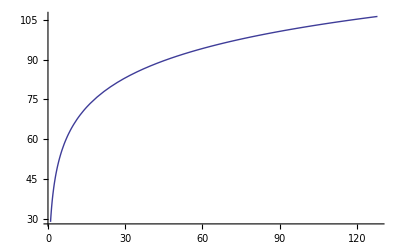

```mathematica
Plot[28.754748311827665+15.991628587175247 Log[c],{c,1,128}]
```

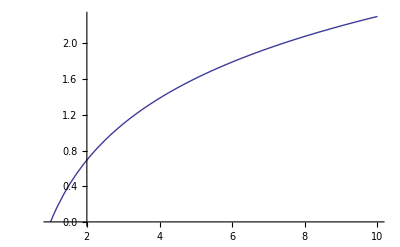

```mathematica
Plot[Log[x],{x,1,10}]
```

1+4/85 Abs[255/2-c]

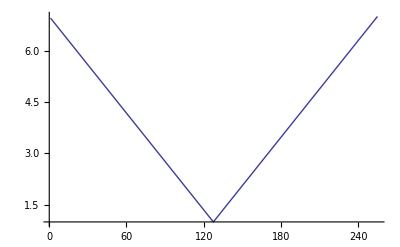

```mathematica
e[c_]=Abs[255/2-c] (6/(255/2)) +1
Plot[e[c],{c,1,255}]
```

```mathematica
npts=Map[({x/.#[[2]],#[[1]]})&,pts];
```

```mathematica
N[pts[[1;;5]]]
N[npts[[1;;5]]]
```

{{7.10517,{x→145.213}},{7.05194,{x→145.368}},{6.99872,{x→145.526}},{6.94553,{x→145.685}},{6.89235,{x→145.846}}}

{{145.213,7.10517},{145.368,7.05194},{145.526,6.99872},{145.685,6.94553},{145.846,6.89235}}

```mathematica
D[(dMax-dMin) ((sMin-x)/(sMax-sMin)+(-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]+Erf[(√2 (c-x))/(3 √(dMax-dMin) √(sMax-sMin))])/(Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))])),x]==0
```

(dMax-dMin) (-1/(sMax-sMin)-(2 ⅇ^(-(2 (c-x)^2)/(9 (dMax-dMin) (sMax-sMin))) √(2/π))/(3 √(dMax-dMin) √(sMax-sMin) (Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))])))

```mathematica
Simplify[(3 √(dMax-dMin) √(sMax-sMin) (Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))/(2 (sMax-sMin) √(2/π))]== ⅇ^(-(2 (c-x)^2)/(9 (dMax-dMin) (sMax-sMin)))
```

(3 √(dMax-dMin) √(π/2) (Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))/(2 √(sMax-sMin))==ⅇ^(-(2 (c-x)^2)/(9 (dMax-dMin) (sMax-sMin)))

```mathematica
Solve[(3 √(dMax-dMin) √(π/2) (Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))/(2 √(sMax-sMin))==ⅇ^(-(2 (c-x)^2)/(9 (dMax-dMin) (sMax-sMin))),x]
```

{{x→ConditionalExpression[1/2 (2 c-3 √2 √(dMax sMax (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])-dMin sMax (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])-dMax sMin (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])+dMin sMin (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))]))),C[1]∈Integers]},{x→ConditionalExpression[1/2 (2 c+3 √2 √(dMax sMax (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])-dMin sMax (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])-dMax sMin (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))])+dMin sMin (2 ⅈ π C[1]+Log[(4 √(sMax-sMin))/(3 (√(dMax-dMin) √(2 π) Erf[(√2 (c-sMax))/(3 √(dMax-dMin) √(sMax-sMin))]-√(dMax-dMin) √(2 π) Erf[(√2 (c-sMin))/(3 √(dMax-dMin) √(sMax-sMin))]))]))),C[1]∈Integers]}}

```mathematica
DynamicModule[{s=40,c=128,sMin=0,sMax=255,dMin=0,dMax=255},
Panel[Column[{
ValueThumbSlider[{sMin,c,sMax}, {0, 255,1}],
ValueThumbSlider[{dMin,dMax}, {0, 255,1}],
ValueThumbSlider[{s}, {N[1/√2], 512}],
Panel[Dynamic[Plot[{dis[ x,s,c,sMin,sMax,dMin,dMax],diag[x,sMin,sMax,dMin,dMax]},{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{dMin,dMax}}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
DynamicModule[{s=40,c=128,sMin=0,sMax=255,dMin=0,dMax=255},
Panel[Column[{
ValueThumbSlider[{sMin,c,sMax}, {0, 255,1}],
ValueThumbSlider[{dMin,dMax}, {0, 255,1}],
ValueThumbSlider[{s}, {N[1/√2], 512}],
Panel[Dynamic[Plot[{dis[ x,s,c,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax]},{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
Simplify[dis[ x,s,c,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax]]
```

dMin+(-dMin sMax+dMax sMin)/(sMax-sMin)+((-dMax+dMin) x)/(sMax-sMin)+((dMax-dMin) (-Erf[(-c+sMin)/(√2 s)]+Erf[(-c+x)/(√2 s)]))/(Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)])

Solve when c = (sMax+sMin)/2 for best case and sMin=0

```mathematica
Simplify[dis[ x,s,(sRange)/2,0,0+sRange,0,0+dRange]-diag[x,0,0+sRange,0,0+dRange]]
```

1/2 dRange (1-(2 x)/sRange+Erf[(-sRange/2+x)/(√2 s)]/Erf[sRange/(2 √2 s)])

```mathematica
DynamicModule[{s=1.5 255,sRange=255,dRange=255},
Panel[Column[{
ValueThumbSlider[{sRange}, {0, 255,1}],
ValueThumbSlider[{dRange}, {0, 255,1}],
ValueThumbSlider[{s}, {N[1/√2], 512}],
Panel[Dynamic[Plot[{1/2 dRange (1-(2 x)/sRange+Erf[(-sRange/2+x)/(√2 s)]/Erf[sRange/(2 √2 s)])},{x,0,sRange},Frame -> True,PlotRange -> {{0,sRange},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
sdMax=128;
DynamicModule[{s=1.5 sdMax,sRange=sdMax,sdRatio=1,dRange},
Panel[Column[{
ValueThumbSlider[{sRange}, {0, sdMax,1}],
ValueThumbSlider[{sdRatio}, {N[1/sdMax], 1,N[1/sdMax]}],
ValueThumbSlider[{s}, {1, N[2 sdMax],1}],
Panel[Dynamic[Plot[{dRange=sdRatio sRange;1/2 dRange (1-(2 x)/sRange+Erf[(-sRange/2+x)/(√2 s)]/Erf[sRange/(2 √2 s)])},{x,0,sRange},Frame -> True,PlotRange -> {{0,sRange},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
Clear[dRange,sdRatio]
```

```mathematica
Simplify[1/2 dRange (1-(2 x)/sRange+Erf[(-sRange/2+x)/(√2 s)]/Erf[sRange/(2 √2 s)])/. {dRange->sdRatio sRange, s-> σ sRange, x-> ξ sRange}]
```

1/2 sdRatio sRange (1-2 ξ+Erf[(-1+2 ξ)/(2 √2 σ)]/Erf[1/(2 √2 σ)])

```mathematica
DynamicModule[{σ=1,sRange=sdMax,sdRatio=1,dRange},
Panel[Column[{
ValueThumbSlider[{sRange}, {0, sdMax,1}],
ValueThumbSlider[{sdRatio}, {N[1/sdMax], 1,N[1/sdMax]}],
ValueThumbSlider[{σ}, {0, 1}],
Panel[Dynamic[Plot[{1/2 sdRatio sRange (1-2 ξ+Erf[(-1+2 ξ)/(2 √2 σ)]/Erf[1/(2 √2 σ)])},{ξ,0,1},Frame -> True,PlotRange -> {{0,sRange},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

Solve when c = 0 for worst case

```mathematica
Simplify[dis[ x,s,sMin,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax]]
```

(dMax-dMin) ((sMin-x)/(sMax-sMin)+Erf[(-sMin+x)/(√2 s)]/Erf[(sMax-sMin)/(√2 s)])

```mathematica
DynamicModule[{s=40,c=128,sMin=0,sMax=255,dMin=0,dMax=255},
Panel[Column[{
ValueThumbSlider[{sMin,c,sMax}, {0, 255,1}],
ValueThumbSlider[{dMin,dMax}, {0, 255,1}],
ValueThumbSlider[{s}, {N[1/√2], 512}],
Panel[Dynamic[Plot[{(dMax-dMin) ((sMin-x)/(sMax-sMin)+Erf[(-sMin+x)/(√2 s)]/Erf[(sMax-sMin)/(√2 s)])},{x,sMin,sMax},Frame -> True,PlotRange -> {{sMin,sMax},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
DynamicModule[{s=40,c=128,sMin=0,sMax=255,dMin=0,dMax=255},
Panel[Column[{
ValueThumbSlider[{sMin,c,sMax}, {0, 255,1}],
ValueThumbSlider[{dMin,dMax}, {0, 255,1}],
ValueThumbSlider[{s}, {N[1/√2], 512}],
Panel[Dynamic[Plot[{(sMin-x)/(sMax-sMin),Erf[(-sMin+x)/(√2 s)]/Erf[(sMax-sMin)/(√2 s)]},{x,sMin,sMax},Frame -> True,PlotRange -> {{sMin,sMax},Automatic}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
D[dis[ x,s,sMin,sMin,sMax,dMin,dMax]-diag[x,sMin,sMax,dMin,dMax],x]==0
Assuming[sMax>sMin&&dMax>dMin&&s≠0,Simplify[Solve[%,x]]]
```

-(dMax-dMin)/(sMax-sMin)+((dMax-dMin) ⅇ^(-(-sMin+x)^2/(2 s^2)) √(2/π))/(s Erf[(sMax-sMin)/(√2 s)])==0

{{x→ConditionalExpression[sMin-√2 s √(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]),C[1]∈Integers]},{x→ConditionalExpression[sMin+√2 s √(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]),C[1]∈Integers]}}

so the maximum is at

```mathematica
x=sMin+√2 s √Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]
```

```mathematica
FullSimplify[dis[ sMin+√2 s √Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])],s,sMin,sMin,sMax,dMin,dMax]-diag[sMin+√2 s √Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])],sMin,sMax,dMin,dMax]]
```

((dMax-dMin) Erf[√Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]])/Erf[(sMax-sMin)/(√2 s)]+((-dMax+dMin) s √(Log[2/π]+2 Log[(sMax-sMin)/(s Erf[(sMax-sMin)/(√2 s)])]))/(sMax-sMin)

```mathematica
DynamicModule[{sMin=0,sMax=255,dMin=0,dMax=255},
Panel[Column[{
ValueThumbSlider[{sMin,sMax}, {0, 255,1}],
ValueThumbSlider[{dMin,dMax}, {0, 255,1}],
Panel[Dynamic[Plot[{((dMax-dMin) Erf[√Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]])/Erf[(sMax-sMin)/(√2 s)]+((-dMax+dMin) s √(Log[2/π]+2 Log[(sMax-sMin)/(s Erf[(sMax-sMin)/(√2 s)])]))/(sMax-sMin),2},{s,0,4 255},Frame -> True,PlotRange -> {{0,2},{0,2}}]],ImageSize->Scaled[1],Alignment->Center ]}],ImageSize->Scaled[.5]]

]
```

```mathematica
Solve[((dMax-dMin) Erf[√Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]])/Erf[(sMax-sMin)/(√2 s)]+(√2 (-dMax+dMin) s √Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])])/(sMax-sMin)==2,s]
```

```mathematica
condit[sMin_,sMax_,dMin_,dMax_]:=((dMax-dMin) Erf[√Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])]])/Erf[(sMax-sMin)/(√2 s)]+(√2 (-dMax+dMin) s √Log[(√(2/π) (sMax-sMin))/(s Erf[(sMax-sMin)/(√2 s)])])/(sMax-sMin)==2
```

```mathematica
NSolve[condit[0,1,0,1],s]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[Erf[√Log[(√(2/π))/(s Erf[1/(√2 s)])]]/Erf[1/(√2 s)]-√2 s √Log[(√(2/π))/(s Erf[1/(√2 s)])]==2,s]

```mathematica
dis[ c+√2 s √(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]))]),s,c,sMin,sMax,dMin,dMax]-diag[c+√2 s √(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]))]),sMin,sMax,dMin,dMax]
```

dMin-(dMin sMax-dMax sMin)/(sMax-sMin)+((dMax-dMin) (-Erf[(-c+sMin)/(√2 s)]+Erf[√(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]))])]))/(Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)])-((dMax-dMin) (c+√2 s √(2 ⅈ π C[1]+Log[(√(2/π) (sMax-sMin))/(s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]))])))/(sMax-sMin)

```mathematica
dis[ x,s,c,sMin,sMax,dMin,dMax]- (dMax-dMin)/(sMax-sMin)
```

dMin+((dMax-dMin) (-Erf[(-c+sMin)/(√2 s)]+Erf[(-c+x)/(√2 s)]))/(Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)])

```mathematica
Plot[dis[ x,s,c,sMin,sMax,dMin,dMax],{c,sMin,sMax},PlotRange->{{sMin,sMax},{0.9 s,2 s}}]
```

```mathematica
cond=(D[dis[ x,s,c,sMin,sMax,dMin,dMax],x]/.x->c) == (dMax-dMin)
```

((dMax-dMin) √(2/π))/(s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]))==dMax-dMin

```mathematica
cond=√(2/π)==s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)])
Solve[%,s]
```

√(2/π)==s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)])

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[√(2/π)==s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]),s]

```mathematica
Simplify[cond/.c->(sMax+sMin)/2]
```

2 s Erf[(sMax-sMin)/(2 √2 s)]==√(2/π)

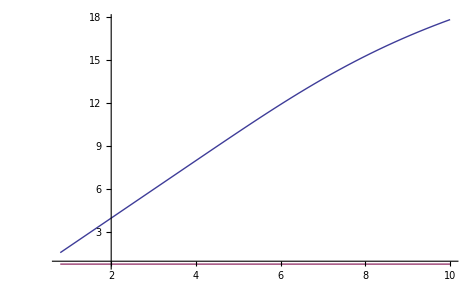

```mathematica
Plot[{2 s Erf[(sMax-sMin)/(2 √2 s)],√(2/π)},{s,√(2/π),10},PlotRange->{{√(2/π),10}]
```

```mathematica
sMin=0;sMax=32;N[Erf[(sMax-sMin)/(2 √2 s)]]
s=√(2/π)
```

1.

√(2/π)

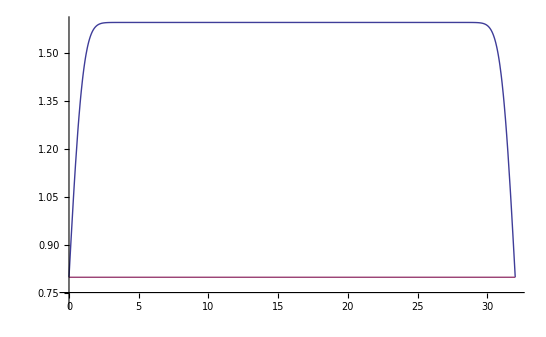

```mathematica
s=√(2/π);sMin=0;sMax=32;
Plot[{s (Erf[(-c+sMax)/(√2 s)]-Erf[(-c+sMin)/(√2 s)]),√(2/π)},{c,sMin,sMax},PlotRange->{{sMin,sMax},{0.9 s,2 s}}]
Clear[s,sMin,sMax]
```

```mathematica
gradC[  σ,μ,0,1,0,1]==(dMax-dMin)/1
```

-(√(2/π))/(σ (Erf[(-1+μ)/(√2 σ)]-Erf[μ/(√2 σ)]))==dMax-dMin

the upper and lower values are at μ = 0 and μ = 0.5

```mathematica
{σ Erf[1/(√2 σ)]==√(2/π),2 σ Erf[1/(2 √2 σ)]==√(2/π)}
```

{σ Erf[1/(√2 σ)]==√(2/π),2 σ Erf[1/(2 √2 σ)]==√(2/π)}

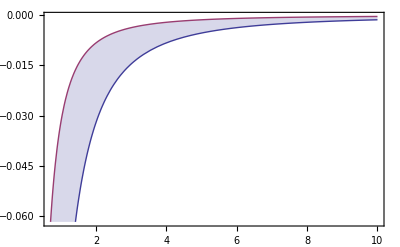

```mathematica
Plot[{σ Erf[1/(√2 σ)]-√(2/π),2 σ Erf[1/(2 √2 σ)]-√(2/π)},{ σ ,1/(√2),10},PlotRange->{{1/(√2),10},{0,-√(2/π)+√2 Erf[1/2]}},Frame->True,Filling->{1->{2}}]
```

This is why in the code we use g = 1/(√2 σ)
1/√2 < σ < ∞
0 < μ< 1
0<g<1

We also define the range scaling ratio as
k = sRange / dRange.
as the src range is always greater than the destination k ≥ 1